```mathematica
ClearAll["Global`*"]
```

```mathematica
namespace = StringJoin[{$HomeDirectory,"/PATH TO REPOSITORY FOLDER"}]
```

```mathematica
g1c1coordsdata = Import[StringJoin[namespace,"/data/simdata/g1c1coords_zeta.csv"]]
```

{{zeta,g1,c1,reserveratiodem},{1.,0.930093,0.78478,1.36583},{1.5,0.936293,0.784664,1.40939},{2.,0.928638,0.785015,1.35495},{2.15,0.859993,0.753829,1.02844}}

```mathematica
g1c1coordsdata//MatrixForm
```

(zeta | g1 | c1 | reserveratiodem
1. | 0.930093 | 0.78478 | 1.36583
1.5 | 0.936293 | 0.784664 | 1.40939
2. | 0.928638 | 0.785015 | 1.35495
2.15 | 0.859993 | 0.753829 | 1.02844)

```mathematica
g1c1coords = Transpose[{g1c1coordsdata[[2;;All,2]],g1c1coordsdata[[2;;All,3]]}]
```

{{0.930093,0.78478},{0.936293,0.784664},{0.928638,0.785015},{0.859993,0.753829}}

```mathematica
g1c1coords//MatrixForm
```

(0.930093 | 0.78478
0.936293 | 0.784664
0.928638 | 0.785015
0.859993 | 0.753829)

```mathematica
phidem = 1 - (c1-g1)/(gammastar - g1)-demcost
```

1-demcost-(c1-g1)/(-g1+gammastar)

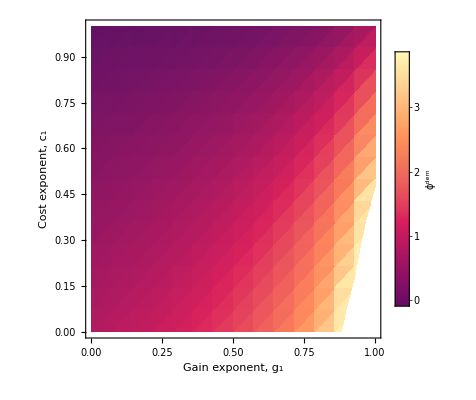

```mathematica
DensityPlot[
Evaluate@(phidem/. {gammastar->1.17,demcost->0.24}),{g1,0,1},{c1,0,1},
FrameLabel->{"Gain exponent, g_1","Cost exponent, c_1"},
LabelStyle->Directive[FontSize->16],
(*---draw the boundary g1==c1--------------------------------*)MeshFunctions->Function[{g1,c1,z},g1-c1],(*what to contour*)
Mesh->{{0}},(*the value to contour*)
MeshStyle->{Thick,Black,Dashed},
(*colour bar with its own label*)PlotLegends->Placed[BarLegend[Automatic,LegendLabel->Style["ϕ^dem"]   (*what to print beside the bar*)],Right]
]
```

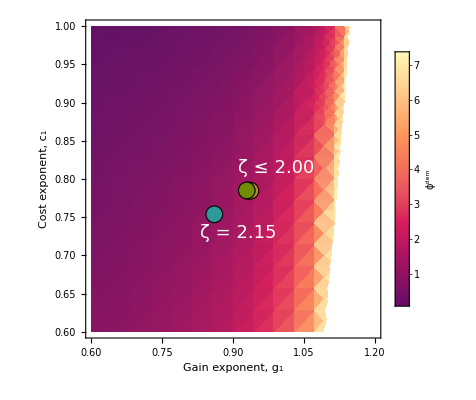

```mathematica
(*your density plot,unchanged except wrapped in a symbol so we can reuse it*)

dp=DensityPlot[Evaluate@(phidem/. {gammastar->1.17,demcost->0.24}),{g1,0.6,1.2},{c1,0.6,1},FrameLabel->{"Gain exponent, g_1","Cost exponent, c_1"},LabelStyle->Directive[Black,FontSize->16],MeshFunctions->Function[{g1,c1,z},g1-c1],Mesh->{{0}},MeshStyle->{Thick,White,Dashed},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->Style["ϕ^dem"]],Right]
];
cols=Table[ColorData[86,i],{i,4}];
(*turn each point into a coloured primitive*)
(*pts=MapThread[{#1,PointSize[0.025],Point[#2]}&,{cols,g1c1coords}];*)

coords=g1c1coords;                (*just to shorten the name*)

(*overlay=Graphics@Join[{Black,PointSize[0.052],Point[coords]},MapThread[{#1,PointSize[0.04],Point[#2]}&,{cols,coords}]
];*)

(*overlay=Graphics@MapThread[{EdgeForm[{Thick,Black}],#1,Disk[#2,0.01]}&,{cols,coords}];
*)
overlay=Graphics@MapThread[{EdgeForm[{Thick,Black}],#1,Disk[#2,Offset[6]]}&,(*6 pt≈2 mm*){cols,coords}];

ReserveRatioDemPlot = Show[
dp,
overlay,
Graphics[Text[Style["ζ = 2.15",FontSize->18, White],{0.91,0.73}]],
Graphics[Text[Style["ζ ≤ 2.00",FontSize->18, White],{0.99,0.815}]],
ImageSize->400
]
(*--optional labels-- Black,MapThread[(Callout[#1,Style[#2,14]])&,{g1c1coords,Range@Length[g1c1coords]}]         (*“1”,“2”,…*)*)
```

```mathematica
Export[StringJoin[namespace,"/rawfigures/fig_reserveratiodem.pdf"],ReserveRatioDemPlot]
Export[StringJoin[namespace,"/rawfigures/fig_reserveratiodem.png"],ReserveRatioDemPlot,ImageResolution->700]
```

```mathematica
coords
```

{{0.930093,0.78478},{0.936293,0.784664},{0.928638,0.785015},{0.859993,0.753829}}

How does failing to reach 37% gain surplus relative to costs impact scaling?

```mathematica
gamma = gammastar/.FullSimplify[Solve[ϕdem== 1 - (c1-g1)/(gammastar - g1)-demcost,gammastar]][[1]]
```

g1+(-c1+g1)/(-1+demcost+ϕdem)

```mathematica
phidem
```

1-demcost-(c1-g1)/(-g1+gammastar)

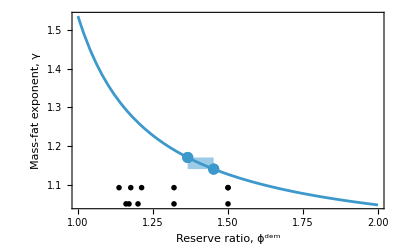

```mathematica
GammaReserveRatioPlot =Show[
Plot[gamma/.{g1->coords[[1,1]],c1->coords[[1,2]],demcost->0.24},{ϕdem,1,2},
Frame->True,
FrameLabel->{"Reserve ratio, ϕ^dem","Mass-fat exponent, γ"},
LabelStyle->Directive[Black,FontSize->16]],
ListPlot[{{phidem/. {gammastar->1.17,demcost->0.24,g1->coords[[1,1]],c1->coords[[1,2]]},1.17}},PlotStyle->Directive[PointSize[0.02]]],
ListPlot[{{phidem/. {gammastar->1.14,demcost->0.24,g1->coords[[1,1]],c1->coords[[1,2]]},1.14}},PlotStyle->Directive[PointSize[0.02]]],
(*ListLinePlot[{{1.31,1.17},{1.42,1.17}}],*)
Graphics[{Directive[ColorData["DefaultPlotColors",1],Opacity[0.5]],Rectangle[{phidem/. {gammastar->1.17,demcost->0.24,g1->coords[[1,1]],c1->coords[[1,2]]},1.14},{phidem/. {gammastar->1.14,demcost->0.24,g1->coords[[1,1]],c1->coords[[1,2]]},1.17}]}],
ycoord = 1.05;
ListPlot[{{1.16,ycoord},{1.20,ycoord},{1.17,ycoord},{1.32,ycoord},{1.50,ycoord}},PlotStyle->Directive[Black],PlotMarkers->{Style["↓",16],Automatic}],
(*Moose*)
ListPlot[{{1.50,ycoord*(1+0.04)}},PlotStyle->Directive[Black],PlotMarkers->{Style["B",16],Automatic}],
ListPlot[{{1.16*(1-0.02),ycoord*(1+0.04)},{1.20*(1+0.01),ycoord*(1+0.04)}},PlotStyle->Directive[Black],PlotMarkers->{Style["K",16],Automatic}],
ListPlot[{{1.17*(1+0.005),ycoord*(1+0.04)},{1.32,ycoord*(1+0.04)}},PlotStyle->Directive[Black],PlotMarkers->{Style["M",16],Automatic}],
ImageSize->400
]
```

```mathematica
phidem/. {gammastar->1.17,demcost->0.24,g1->coords[[1,1]],c1->coords[[1,2]]}
```

1.3657

```mathematica
gamma/.{g1->coords[[1,1]],c1->coords[[1,2]],demcost->0.24,ϕdem->}
```

1.15407

```mathematica
Export[StringJoin[namespace,"/rawfigures/fig_reserveratiodem_gamma.pdf"],GammaReserveRatioPlot]
```

```mathematica
CombinedReservePlot = GraphicsColumn[{
ReserveRatioDemPlot,
GammaReserveRatioPlot
}]
```

-Graphics-

```mathematica
Export[StringJoin[namespace,"/rawfigures/fig_reserveratiodem_2panel.png"],CombinedReservePlot, ImageResolution->700]
```

Examine phi and phidem for gamma +- SE

```mathematica
GammaUpperSE = 1.171 + 0.023
GammaLowerSE = 1.171 - 0.023
```

1.194

1.148

```mathematica
phiUpperSE = 1 - (c1 - g1)/(gammastar - g1)/.{g1->coords[[1,1]],c1->coords[[1,2]],gammastar->GammaUpperSE}
phiLowerSE = 1 - (c1 - g1)/(gammastar - g1)/.{g1->coords[[1,1]],c1->coords[[1,2]],gammastar->GammaLowerSE}
```

1.55062

1.66686

```mathematica
phidemUpperSE = 1 - (c1 - g1)/(gammastar - g1)-demcost/.{g1->coords[[1,1]],c1->coords[[1,2]],gammastar->GammaUpperSE,demcost -> 0.24}
phidemLowerSE = 1 - (c1 - g1)/(gammastar - g1)-demcost/.{g1->coords[[1,1]],c1->coords[[1,2]],gammastar->GammaLowerSE,demcost -> 0.24}
```

1.31062

1.42686